```mathematica
others = Plot[
{1/(x^2+1),D[1/(n^2+1),{n,2}]/.n->x},
{x,-5,5},
PlotRange->{{-5,5},{-2.1,1.1}},
AspectRatio->1/2,
PlotStyle->{{Black,Dashed},Black},
ImageSize->Large,
Ticks->None
];
```

```mathematica
dotted = Plot[
D[1/(n^2+1),n]/.n->x,
{x,-5,5},
PlotStyle->{White, Thin},
Ticks->None,
PlotRange->{{-5,5},{-2.1,1.1}},
AspectRatio->1/2,
Mesh->75,
ImageSize->Large,
MeshStyle->{Black, PointSize@0.0075},
MeshFunctions->{"ArcLength"}
];
```

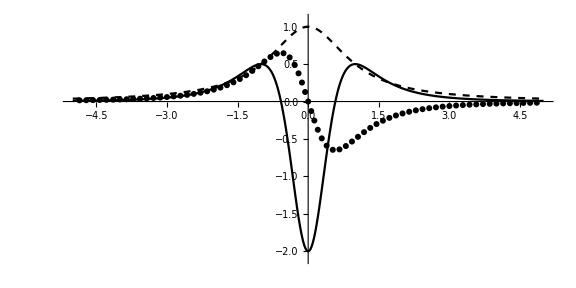

```mathematica
Show[dotted,others]
```